```mathematica
(* after running visio.nb run Init data, rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ], Error Estimation*)
```

### Init data

```mathematica
ρ0=1;
u0 = 0;
L1=Lx;
L2=Ly;
γ=1.4;
c=1;
f=0.5;
w = 2π f;
off = 5;
k = w/c;
a=10^-3;
timeP = 3;
```

### Analytical solutions for density, velocity, pressure, energy

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=a Cos[w t - k x]+ρ0
```

```mathematica
rhoAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=a*(Exp[-(x -off - c t)^2]+Exp[-(x - off+ c t)^2])/2+ρ0
(*uAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=-a Sin[w t - k x]+u0*)
vAn[x_?NumberQ,y_?NumberQ,t_?NumberQ]:=(eps(y-L2/2))/(2alphaa √((x-L1/2)^2+(y-L2/2)^2))NIntegrate[Exp[-ξ^2/(4alphaa)]Sin[ξ t]BesselJ[1,ξ √((x-L1/2)^2+(y-L2/2)^2)]ξ,{ξ,0,∞}]
```

```mathematica
mcrCenterLine=MeshCellRcm[[nx ny/2+1;;nx ny/2+nx]];
```

```mathematica
mmm=Table[MeshCellRcm[[i]],{i,MeshCellRcm//Length}];
```

```mathematica
rhoAn[mmm[[1,1]],mmm[[1,2]],2.0]
```

NIntegrate::maxp: The integral failed to converge after 517 integrand evaluations. NIntegrate obtained 2.05202×10^-10 and 1.4803×10^-7 for the integral and error estimates.

5.13005×10^-17

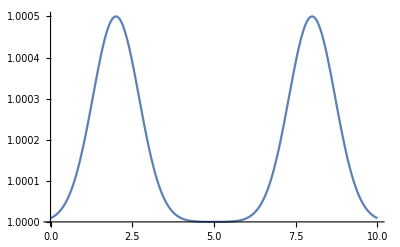

```mathematica
angr=Plot[rhoAn[x,0,timeP],{x,0,Lx}]
```

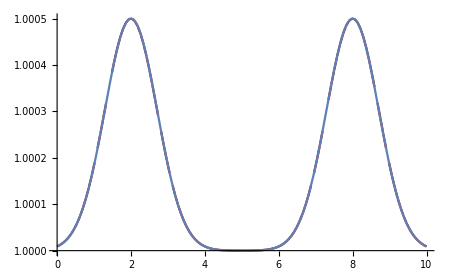

```mathematica
Show[fig2,angr]
```

### Center values for graphics

```mathematica
dataAnCenterRhoEqP=ParallelTable[{mmm[[i,1]],rhoAn[mmm[[i,1]],mmm[[i,2]],timeP]+1},{i,mcrCenterLine//Length}];
dataAnCenterU=ParallelTable[{mmm[[i,1]],uAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
dataAnCenterV=ParallelTable[{mmm[[i,1]],vAn[mmm[[i,1]],mmm[[i,2]],timeP]},{i,mcrCenterLine//Length}];
```

```mathematica
dataAnCenterE=Transpose@{dataAnCenterRhoEqP[[All,1]],dataAnCenterRhoEqP[[All,2]]/(γ-1)+1/2 dataAnCenterRhoEqP[[All,2]](dataAnCenterU[[All,2]]*dataAnCenterU[[All,2]] + dataAnCenterV[[All,2]]*dataAnCenterV[[All,2]])};
```

```mathematica
dataAnCenterH=Transpose@{dataAnCenterRhoEqP[[All,1]],1/dataAnCenterRhoEqP[[All,2]](dataAnCenterE[[All,2]] + dataAnCenterRhoEqP[[All,2]])};
```

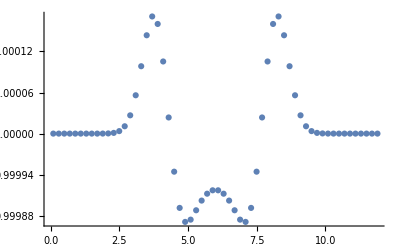

```mathematica
dataExact=ListPlot[dataAnCenterRhoEqP,PlotRange->All]
```

### Error Estimation

```mathematica
cellQuarter=Flatten[Table[MeshCellRcm[[i*nx+j]],{i,0,0.5ny-1},{j,1,0.5nx}],1];
```

```mathematica
cellNodes=Table[{
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]-hy/2},
{MeshCellRcm[[i,1]]+hx/2,MeshCellRcm[[i,2]]+hy/2},
{MeshCellRcm[[i,1]]-hx/2,MeshCellRcm[[i,2]]+hy/2}},
{i,(MeshCellRcm//Length)}];
```

```mathematica
cells=Table[Polygon[cellNodes[[i]]],{i,1,cellNodes//Length}];
cells[[1]]
```

Polygon[{{0.,0.},{0.078125,0.},{0.078125,1.},{0.,1.}}]

```mathematica
Clear[cellNodes]
```

```mathematica
fDiffer[x_,y_,t_,n_]:=Abs[rhoAn[x,y,t]-GetSol[alpha,n,1,{x,y}]/1]
```

#### NormC

```mathematica
NMaxValue[{fDiffer[x,y,timeP,1],{x,y}∈cells[[1]]},{x,y}]
```

2.63842×10^-7

```mathematica
maxitable=ParallelTable[NMaxValue[{fDiffer[x,y,timeP,n],{x,y}∈cells[[n]]},{x,y}],{n,1,cellNodes//Length}];
maxitable[[1]]
```

NMaxValue::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

2.63842×10^-7

```mathematica
Max[maxitable]
```

```mathematica
1.0779134802518797*^-6
```

```mathematica
5.329088987870989*^-7
```

```mathematica
5.2924977755886*^-7
```

```mathematica
5.292491973563074*^-7
```

#### Norm L1

```mathematica
NIntegrate[fDiffer[x,y,timeP,1],{x,y}∈cells[[1]],
WorkingPrecision->15 ,MaxPoints->2000]
```

9.78349755876276×10^-7

```mathematica
intable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n],{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
intable[[1]]
```

9.78349755876276×10^-7

```mathematica
Sum[intable[[i]],{i,intable//Length}]
```

0.000500231009804709

#### Norm L2

```mathematica
(*надо переделать - квадрат возмущения считают по всей расчетной области*)
```

```mathematica
insqrtable=ParallelTable[NIntegrate[fDiffer[x,y,timeP,n]^2,{x,y}∈cells[[n]],MaxRecursion->5,AccuracyGoal->5,PrecisionGoal->5,WorkingPrecision->15 ,MaxPoints->2000],{n,1,cellNodes//Length}];
insqrtable[[1]]
```

9.42122560599295×10^-24

```mathematica
√Sum[insqrtable[[i]],{i,insqrtable//Length}]
```

```mathematica
8.0061403970885980209334252486821`15.301029995663974*^-7
```

```mathematica
4.4030290576288594175615632742439`15.301029995663981*^-7
```

```mathematica
8.097684201245305212998232964007`15.301029995663962*^-8
```

```mathematica
2.4485155921685051401437828656416`15.301029995663969*^-7
```

```mathematica
8.295058830784622 ^-8
```